# Bead in a Standing Wave

```mathematica
m = 2.65*10^3*4/3 π (0.5*10^-6)^3;
DragCoeff = 10^-8;
c = 1484;
λ = 0.008;
F = 100 10^-12;
```

```mathematica
F[x,t] == m*x''[t]
```

```mathematica
F[x,t] = Fnot*Sin[x]*Sin[t];
```

```mathematica
A = Fnot/m;
```

```mathematica
Control[{A,0,0.1}]
```

Inertia is significant (high Reynold’s number).

{{x[t]→InterpolatingFunction[{{0.,1.}},<>][t]}}

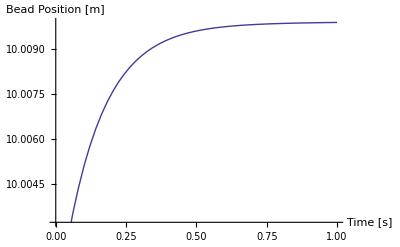

```mathematica
s=NDSolve[{10^-6/10^-12 x''[t] == DragCoeff/m*(F/DragCoeff*Sin[(2π)/λ*10^-6*x[t]]*Sin[2π*c/λ*10^-6*t]-
x'[t]),x[0] == 10, x'[0] == A},x[t],{t,0,1}]
Plot[x[t]/.s,{t,0,1},AxesLabel-> {"Time [s]","Bead Position [m]"}]
```

Inertia is insignificant (low Reynold’s number).

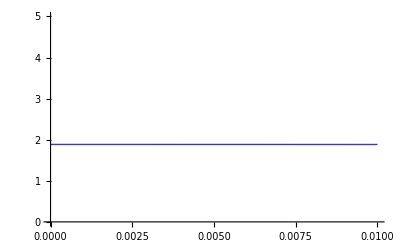

```mathematica
s=NDSolve[{x'[t] == A*Sin[2π*x[t]]*Sin[2π*t],x[0] == π(0.6)},x[t],{t,0,0.1}];
Plot[x[t]/.s,{t,0,0.01},PlotRange-> {0,5}]
```

```mathematica
DSolve[x'[t] == A*Sin[2π*x[t]]*Sin[2π*t],x[t],t]
```

$Aborted